Random Walks

```mathematica
Histogram[Table[RandomChoice[{-1,0,1}],10000]];
```

```mathematica
temp=Table[RandomChoice[{-1,1}],100];
```

```mathematica
AppendTo[temp,10];
```

```mathematica
AppendTo[temp,100];
```

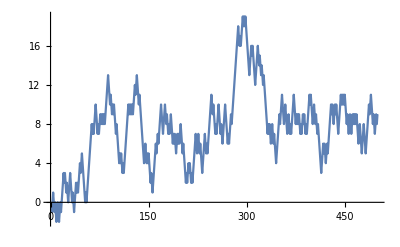

```mathematica
a={0};
Do[AppendTo[a,a[[n-1]]+RandomChoice[{-1,1}]],{n,2,500}];
ListPlot[a,Joined->True]
```

Such Structures are commonly used in the study of polymers, stock prices, series data, and trajectories of Brownian particles. 

Can we verify this, with our numerics? 
Let us try to do so...
      < (m^2)> = N

```mathematica
data=Table[{n,Table[Table[RandomChoice[{-1,1}],{n}]//Total,{1000}]^2//N//Mean},{n,100,1000,100}]
```

{{100,104.74},{200,189.18},{300,291.732},{400,402.488},{500,499.536},{600,634.468},{700,721.052},{800,782.12},{900,870.428},{1000,944.212}}

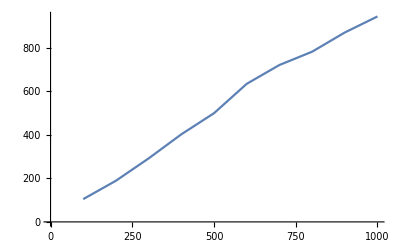

```mathematica
ListPlot[data,Joined->True]
```

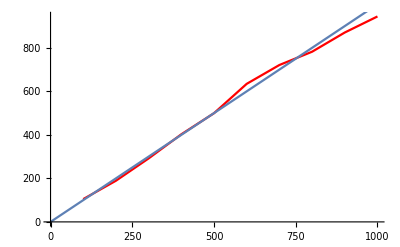

```mathematica
Show[ListPlot[data,PlotStyle->Red, Joined->True],Plot[x,{x,0,1000}]]
```

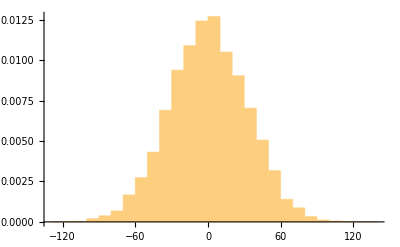

```mathematica
nMax=1000;
binsize=10;
histdata=Histogram[Table[Table[RandomChoice[{1,-1}],{nMax}]//Total,{10000}],{binsize},"PDF"]
```

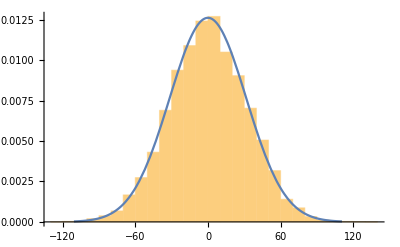

```mathematica
Show[histdata,Plot[1/(√(2π nMax))ⅇ^(-x^2/(2nMax)),{x,-3.5 √nMax,3.5 √nMax}]]
```

The Biased Random Walk

```mathematica
Clear["Global`*"]
```

```mathematica
UnitStep[RandomReal[{0,5}]]
```

1

```mathematica
p=0.99;
```

```mathematica
1-2 UnitStep[RandomReal[]-p]
```

1

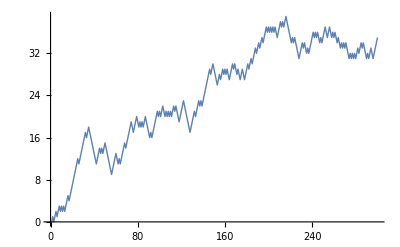

```mathematica
p=0.55  ;
b={0};
Do[AppendTo[b,b[[n-1]]+1-2 UnitStep[RandomReal[]-p]],{n,2,300}];
ListPlot[b,Joined->True, PlotStyle->Thick]
```

In this case, a walk is Biased Random Walk, the speed of going is away from the origin. 
Biased Random Walk, make it move away and away from th Origin. 

For an Biased Random walk, Show, that, 
<m^2> = N(N-1)(2p - (1))^2

```mathematica
p=0.55  ;
np =Table[{n, Table[Table[1-2 UnitStep[RandomReal[]-p],{n}]//Total,{10000}]^2//N //Mean}, {n,1000,10000,1000}];
```

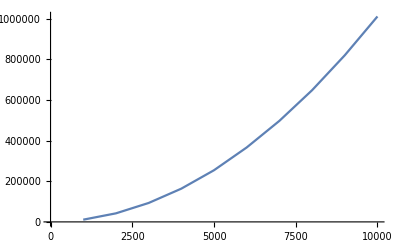

```mathematica
pki = ListPlot[np, Joined->True]
```

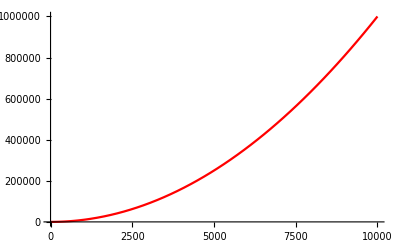

```mathematica
kpi = Plot[x(x-1)(2p - 1)^2, {x,0,10000}, PlotStyle->Red]
```

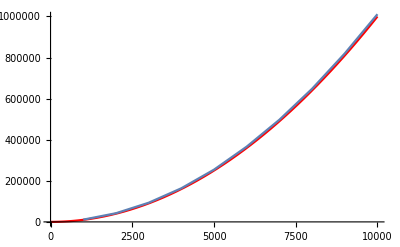

```mathematica
Show[kpi, pki]
```

Random Walk : Mean and Variance of net displacement

Stirling Formula :- 
     ln (n!) = (n + 1/2) ln(n) - n + 1/2 ln(2 π) + O(n^-1)

```mathematica
Log[10]//N
```

2.30259

```mathematica
nasi = Table[(n+1/2) Log[n]-n+1/2 Log[2 π], {n,1,10}]//N//TableForm
```

-0.0810615
0.651806
1.76408
3.15726
4.77085
6.56538
8.51326
10.5942
12.7926
15.0961

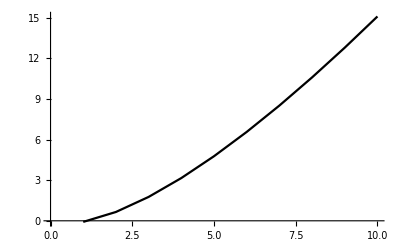

```mathematica
jhansi =ListPlot[Table[(n+1/2) Log[n]-n+1/2 Log[2 π], {n,1,10}], Joined->True, PlotStyle->Black]
```

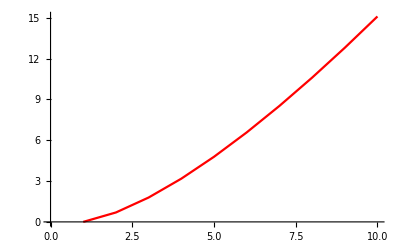

```mathematica
kasi = ListPlot[Table[Log[Factorial[n]], {n,1,10}], Joined->True, PlotStyle->Red]
```

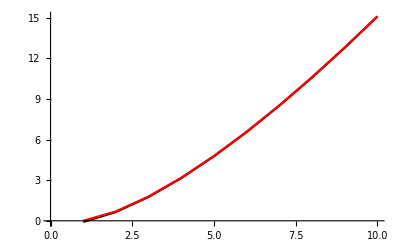

```mathematica
Show[jhansi, kasi]
```

One can us Plot Markers Also, to plot and see the points matching.

```mathematica
Clear["Global`*"]
```

```mathematica
plotexact = ListPlot[Table[Log[Factorial[n]], {n,1,10}], PlotMarkers->Style[ "ⅇ", 14,Red]];
plotapprox = ListPlot[Table[(n+1/2) Log[n]-n+1/2 Log[2 π], {n,1,10}], PlotMarkers->Style[ "ϕ", 14,Blue]];
```

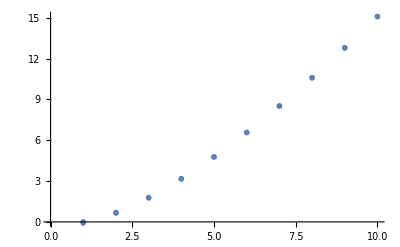

```mathematica
Show[plotexact, plotapprox]
```

Here we checked.

```mathematica
_______________________________________________
```

```mathematica
g1=Table[Factorial[n],{n,1,5}]
```

{1,2,6,24,120}

```mathematica
Total[g1]
```

153

```mathematica
g2=Table[n^n ⅇ^-n,{n,1,5}]//N
```

{0.367879,0.541341,1.34425,4.6888,21.0561}

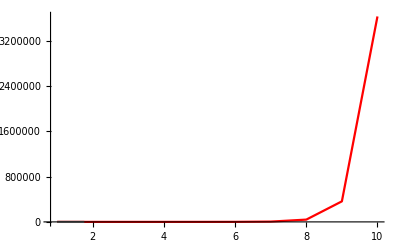

```mathematica
Show[ListPlot[g1,Joined->True,PlotStyle->Red,PlotRange->Full],ListPlot[g2,Joined->True,PlotStyle->Gray,PlotRange->{0.3,0.5}]]
```

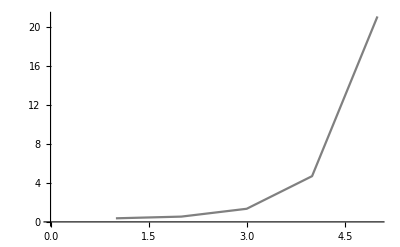

```mathematica
gr1=ListPlot[g2,Joined->True,PlotStyle->Gray]
```

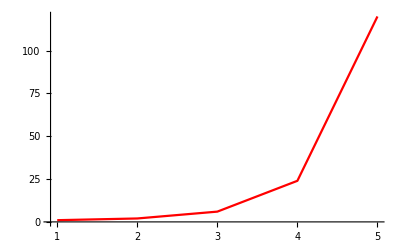

```mathematica
gr2=ListPlot[g1,Joined->True,PlotStyle->Red,PlotRange->Full]
```

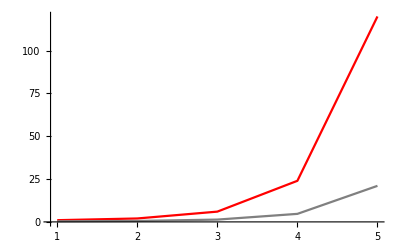

```mathematica
Show[gr2,gr1]
```

-Graphics-

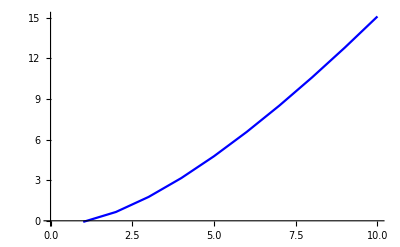

```mathematica
plotexact=ListPlot[Table[Log[Factorial[n]],{n,1,10}],Joined->True,PlotStyle->Red]
plotapprox=ListPlot[Table[Log[n](n+1/2)-n+1/2 Log[2π],{n,1,10}],PlotStyle->Blue,Joined->True]
```

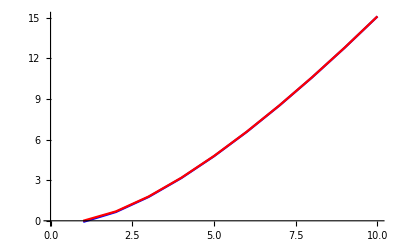

```mathematica
Show[plotapprox,plotexact]
```

```mathematica
________________________________________________
```

```mathematica
Manipulate[Plot[{Factorial[n]/(Factorial[(n+m)/2]Factorial[(n-m)/2])1/2^n,√(2/(π n))ⅇ^(-m^2/(2n))},{m,-n,n}],{n,10,100}]
```

Random Walk-5
Diffusion Equation

```mathematica
Integrate[1/(√(4π Ds t))ⅇ^(-x^2/(4 Ds t)),{x,-Infinity,Infinity}]
```

ConditionalExpression[√(1/(Ds t)) √(Ds t), Re[1/(Ds t)]>0]

This Clearly Indicates it is normalized. 
1/(√(4π Ds t)) as this term is always in multiplication with the given distribution function for Diffusion equation.

```mathematica
Ds=1;
Animate[Plot[1/(√(4π Ds t))ⅇ^(-x^2/(4 Ds t)),{x,-5,5}, PlotRange->{0,1}],{t,0.01,1}]
```

```mathematica
Integrate[x/(√(4π Ds t))ⅇ^(-x^2/(4 Ds t)),{x,-Infinity,Infinity}]
```

ConditionalExpression[0, Re[t]>0]

```mathematica
Integrate[x^2/(√(4π Ds t))ⅇ^(-x^2/(4 Ds t)),{x,-Infinity,Infinity}]
```

ConditionalExpression[2 t, Re[t]>0]

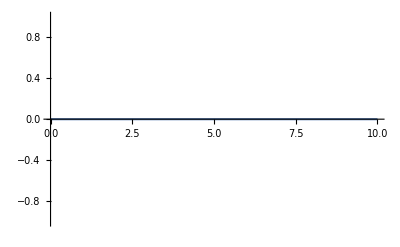

```mathematica
meanplot = Plot[0, {t,0,10}]
```

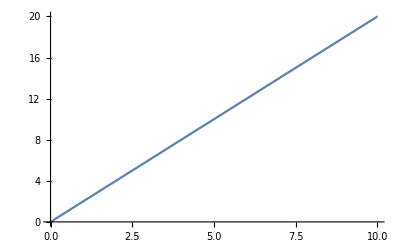

```mathematica
Varianceplot = Plot[2t, {t,0,10}]
```

The more the time elapses, the more the width. Hence, the variance, but its mean remains the same[Centre position]. [SEE QUALITATIVELY FROM THE GRAPH].

Random Walk - : Central Limit Theorem

```mathematica
Clear["Global`*"]
```

```mathematica
a = {0};
Do[AppendTo[a, a[[n-1]] + 1-2RandomReal[]], {n,2,500}]
```

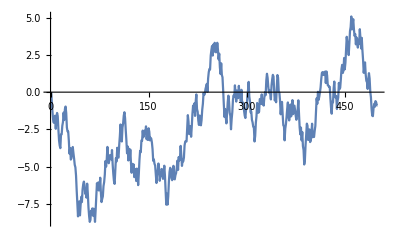

```mathematica
ListPlot[a, Joined->True]
```

```mathematica
data = Table[{n, Table[Table[1-2 RandomReal[], {n}]//Total, {10000}]^2//N//Mean}, {n,100,1000,100}]
```

{{100,33.1886},{200,65.7704},{300,98.7564},{400,134.383},{500,166.805},{600,199.704},{700,234.205},{800,262.54},{900,305.649},{1000,337.552}}

```mathematica
k[x_]=r x;
fit=FindFit[data,{r x},{r},{x}]
```

{r→0.334984}

```mathematica
g[x_]= k[x]/.fit
```

0.334984 x

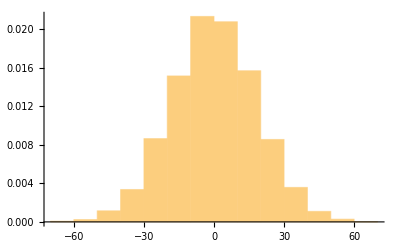

```mathematica
nMax=1000;
binsize=50;
histdata=Histogram[Table[Table[1 - 2RandomReal[],{nMax}]//Total,{10000}],Automatic,"PDF"]
```

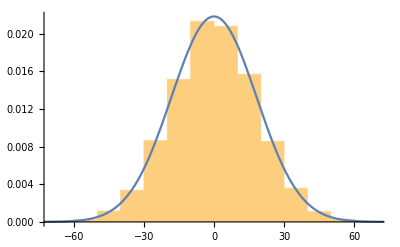

```mathematica
Show[histdata,Plot[(√3)/(√(2π nMax))ⅇ^((-3 x^2)/(2nMax)),{x,-5 √nMax,5 √nMax}]]
```

```mathematica
data = Table[{n,Table[Table[RandomVariate[NormalDistribution[]], {n}]//Total, {10000}]^2//N//Mean}, {n,100,1000,100}]
```

{{100,100.069},{200,200.463},{300,306.897},{400,395.701},{500,487.579},{600,610.227},{700,685.028},{800,795.967},{900,906.087},{1000,1031.35}}

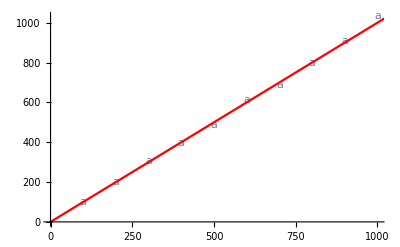

```mathematica
Show[ListPlot[data, PlotMarkers->{"a", 14, Black}],Plot[x,{x,0,1500}, PlotStyle->Red] ]
```

```mathematica
nMax=1000;
binsize=50;
histdata=Histogram[Table[Table[RandomVariate[NormalDistribution[]],{nMax}]//Total,{10000}],Automatic,"PDF"];
```

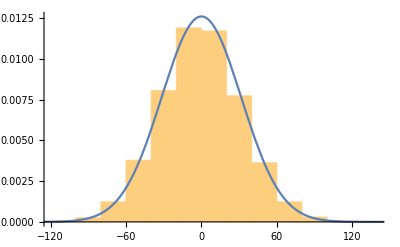

```mathematica
Show[histdata, Plot[√(1/(2π nMax)) ⅇ^(-x^2/(2nMax)), {x,-5 √nMax, 5 √nMax}]]
```

Random Walk 7-: First Passage Problem

```mathematica
Clear["Global`*"]
```

```mathematica
data = Table[num = Table[a = {0};
fp= 0;
Do[AppendTo[a, a[[n-1]] + RandomChoice[{-1,1}]];
If[a[[n]]==0, fp=1;
Break[]], {n,2,nsteps}];
fp, {10000}];
{nsteps, Total[num]/Length[num]//N},
{nsteps, {10,50,100,200,500,1000,2000,5000,10000}}];
```

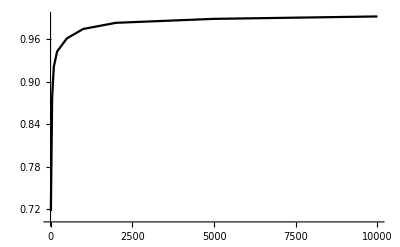

```mathematica
ListPlot[data, Joined->True, PlotStyle->Black]
```

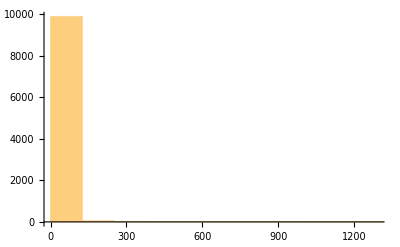

```mathematica
data = Table[a={0};
AppendTo[a, a[[1]] + RandomChoice[{-1,1}]];
n = 2;
While[a[[n]] ≠ 0, 
AppendTo[a, a[[n-1]] + RandomChoice[{-1,1}]]; n++];
tfp = n - 1;
tfp, {10000}];
Tally[data//Sort]//TableForm;
Histogram[data]
```

```mathematica
Mean[data]//N
```

26.8536

```mathematica
means = Table[data = Table[a = {0};
AppendTo[a, a[[1]] + RandomChoice[{-1,1}]];
n = 2;
While[a[[n]]≠ 0, 
AppendTo[a, a[[n-1]] + RandomChoice[{-1,1}]]; n++];
tfp = n - 1;
tfp, {nWalks}];
{nWalks, Mean[data]//N}, {nWalks, 100, 2000, 100}];
```

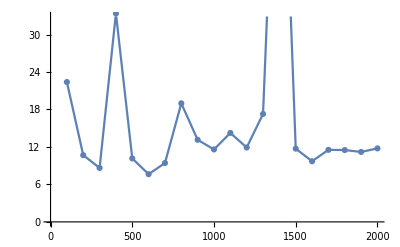

```mathematica
ListPlot[means, Joined->True, PlotMarkers->Automatic]
```

```mathematica
data = Table[a = {0};
AppendTo[a, a[[1]] + RandomChoice[{-1,1}]];
n = 2;
While[a[[n]]≠ 0, 
AppendTo[a, a[[n-1]] + RandomChoice[{-1,1}]]; n++];
tfp = n - 1;
tfp, {10000}];
```

```mathematica
means = Table[Mean[Take[data, n]]//N, {n,1,10000}];
```

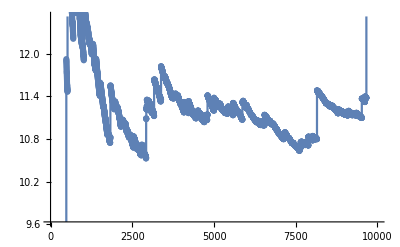

```mathematica
ListPlot[means, Joined->True, PlotMarkers -> Automatic]
```

Overall TakeHome message :- With Probability 1, there is going to be the first passage to the origin or any point that we choose, but the average time taken for first passage is infinity, that is why, this quantity mean is not an convergent quantity.